# Paso I. Variables.

```mathematica
NPart = 20; (*Número de pasos*)
init=1;end = NPart+1;
```

```mathematica
sxVar = Table[sx[i], {i, init, end}]; (*Posición en eje 0X*)
syVar = Table[sy[i], {i, init, end}]; (*Posición en eje 0Y*)
vxVar = Table[vx[i],{i, init, end}]; (*Velocidad en eje 0X*)
```

```mathematica
vyVar = Table[vy[i], {i, init, end}]; (*Velocidad en eje 0Y*)
```

```mathematica
ΛxVar = Table[Λx[i], {i, init, end}]; (*Aceleración artificial en el eje 0X*)
ΛyVar = Table[Λy[i], {i, init, end}]; (*Aceleración artificial en el eje 0Y*)
```

```mathematica
Vars = Join[sxVar, syVar, vxVar, vyVar, ΛxVar, ΛyVar];
```

# Paso II. Parámetros

```mathematica
(*Constante de gravitación universal*)
G=1;
(*Radio de la Tierra*)
roE=2;
(*Radio de la Luna*)
roM=1;
(*Masa de la Tierra*)
mE=10;
(*Masa de la Luna*)
mM=1;
(*Distancia entre el centro de la Tierra y el centro de la Luna*)
a = 20;
(*Vector apunta Tierra*)
rE={0,0};
(*Vector apunta Luna*)
rM={a,0};
(*Ángulo Salida*)
tethaM = Pi/2;
(*Ángulo Llegada*)
tethaE = 3Pi /2;
(*Duración de la trayectoria del vuelo*)
TTT = 14*24*60*60;
TT = 1000;
T=1;
(*Partición del tiempo*)
h=T/NPart;
(*Vector direccional cohete*)
(*rR[t_]:={sx[t],sy[t]}/Sqrt[sx[t]^2+sy[t]^2];*)(*Como función*)
(*Componente apunta cohete en OX*)
rRx = Table[sxVar[[k]]/Sqrt[sxVar[[k]]^2 + syVar[[k]]^2], {k, 1, NPart+1}];
(*Componente direccional cohete en OY*)
rRy = Table[syVar[[k]]/Sqrt[sxVar[[k]]^2 + syVar[[k]]^2], {k, 1, NPart+1}];
(*Distancia Cohete-Tierra*)
dER=Table[Sqrt[sxVar[[k]]^2+syVar[[k]]^2], {k, 1, NPart+1}];
(*Distancia Cohete-Luna*)
dMR=Table[Sqrt[(sxVar[[k]]-a)^2+syVar[[k]]^2], {k, 1, NPart+1}];
(*Componentes direccionales vector Cohete-Luna*)
```

```mathematica
rMRx= Table[(sxVar[[k]]-rM[[1]])/Norm[{sxVar[[k]], syVar[[k]]}-rM, 2], {k, 1, NPart+1}];
rMRy= Table[(syVar[[k]]-rM[[2]])/Norm[{sxVar[[k]], syVar[[k]]}-rM, 2], {k, 1, NPart+1}];
(*Componentes direccionales vector Cohete-Tierra*)
rERx= Table[(sxVar[[k]]-rE[[1]])/Norm[{sxVar[[k]], syVar[[k]]}-rE, 2], {k, 1, NPart+1}];
rERy= Table[(sxVar[[k]]-rE[[2]])/Norm[{sxVar[[k]], syVar[[k]]}-rE, 2], {k, 1, NPart+1}];
```

# Paso III. Restricciones Igualdades. Condiciones Iniciales.

```mathematica
(*3.- Valores iniciales*)
(*Posiciones de salida del cohete*)
sInit = {sxVar[[1]]==    roE*Cos[tethaE], syVar[[1]]==    roE*Sin[tethaE]};
(*--------------------*)
(*Posiciones de llegada del cohete*)
sFinal = {sxVar[[NPart+1]]==   a+ roM*Cos[tethaM], syVar[[NPart+1]]==    roM*Sin[tethaM]};
(*--------------------*)
(*Velocidad de salida*)
v0 =50; (*m/s*)
vInit = {vxVar[[1]]==    v0*Cos[tethaE], vyVar[[1]]==    v0*Sin[tethaE]};
(*--------------------*)
(*Velocidad de llegada*)
vN = 1; (*m/s*)
vFinal = {vxVar[[NPart+1]]==    vN*Cos[tethaM+Pi], vyVar[[NPart+1]]==    vN*Sin[tethaM+Pi]}

(*----------------------------------*)
(*Aceleración de salida y llegada*)
```

{vx[21]==0,vy[21]==-1}

```mathematica
RInit = Join[sInit, sFinal, vInit, vFinal]
```

{sx[1]==0,sy[1]==-2,sx[21]==20,sy[21]==1,vx[1]==0,vy[1]==-50,vx[21]==0,vy[21]==-1}

# Paso IV. Restricciones Desigualdad.

```mathematica
(*Evitar la colisión con la Tierra*)
R1= Table[sxVar[[k]]^2+syVar[[k]]^2≥ roE^2 ,{k,1,NPart+1}];
(* Evitar la conlisión con la Luna*)
R2=Table[(sxVar[[k]]-a)^2+syVar[[k]]^2≥ roM^2,{k,1,NPart+1}];
(*----------------------------------*)

(*_____________________________________*)
(*Primero discretizamos el tiempo y aplicamos el Método Euler Explícito*)
Gx=Table[-((N[mM G]/dMR[[k]]^2)*rMRx[[k]]+(N[mE G]/dER[[k]]^2)*rERx[[k]]), {k, 1, NPart+1}];
Fx[k_]:=Gx[[k]]+ΛxVar[[k]];
(*Parte de la expresión final*)
R3=Table[vxVar[[k+1]]==   vxVar[[k]] + .5 h (Fx[k]+Fx[k+1]),{k,1,NPart}];
Gy=Table[-((N[mM G]/dMR[[k]]^2)*rMRy[[k]]+(N[mE G]/dER[[k]]^2)*rERy[[k]]), {k, 1, NPart+1}];
Fy[k_]:=Gy[[k]]+ΛyVar[[k]];
R4=Table[vyVar[[k+1]]==   .5 (Fy[k]+Fy[k+1])*h+vyVar[[k]],{k,1,NPart}];
```

```mathematica
R5 = Table[sxVar[[k+1]]== (vxVar[[k]] + vxVar[[k+1]])*h/2+sxVar[[k]], {k, 1, NPart}];
R6 = Table[syVar[[k+1]]== (vyVar[[k]]+vyVar[[k+1]])*h*.5+syVar[[k]], {k, 1, NPart}];
R71 = Table[ΛxVar[[k]]≥ -20, {k, 1, NPart+1}];
R72 = Table[ΛxVar[[k]]≤  20, {k, 1, NPart+1}];
R81 = Table[ΛyVar[[k]]≥ -20, {k, 1, NPart+1}];
R82 = Table[ΛyVar[[k]]≤  20, {k, 1, NPart+1}];
```

```mathematica
restrictions = Join[  R3, R4,R5, R6, R71, R72, R81, R82 ,  RInit];
```

# Paso V. Función Objetivo.

```mathematica
(*5) Función Objetivo*)
(*------------------------------------------------------------------------------------*)
Objetive=Sum[Λx[tn]^2+Λy[tn]^2,{tn,1,NPart+1}];
(*Restricciones*)
Timing[SolAlt = FindMinimum[{Objetive, restrictions},Vars];]
```

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

{22.9514,Null}

```mathematica
Plots = Table[{SolAlt[[2, k, 2]], SolAlt[[2, k+NPart+1, 2]]}, {k, 1, NPart+1}]
```

{{0.,-2.},{0.0250013,-4.475},{0.100003,-6.90001},{0.225003,-9.27502},{0.4,-11.6},{0.624995,-13.8751},{0.899988,-16.1001},{1.22498,-18.2751},{1.59997,-20.4001},{2.02495,-22.4751},{2.49994,-24.5002},{3.02493,-26.4752},{14.8243,-2.1666},{15.4492,-1.58607},{16.1242,-1.25498},{16.8492,-0.999936},{17.6244,-0.767501},{18.4499,-0.535001},{19.327,-0.293122},{20.0175,-0.0327385},{20.,1.}}

```mathematica
A = ListLinePlot[Plots, PlotStyle->PointSize[Large]];
```

```mathematica
B =Graphics[Circle[{0, 0}, roE]];
CC =Graphics[Circle[{a, 0}, roM]];
```

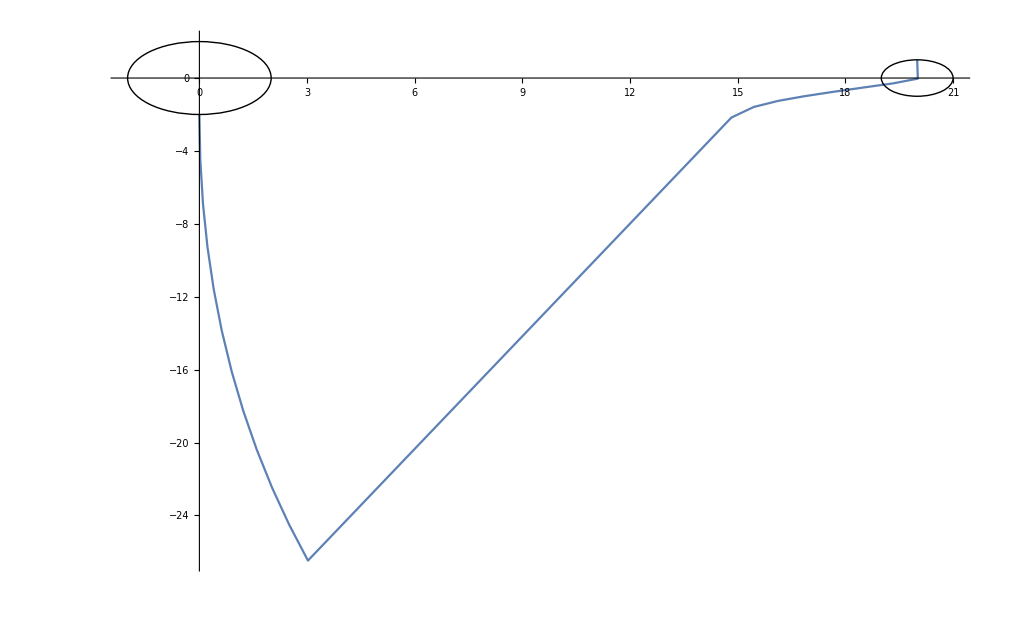

```mathematica
Show[A, B, CC, PlotRange-> All]
```